# photon collection

```mathematica
NA[d_,f_]:=Sin[ArcTan[d/(2 f)]];
```

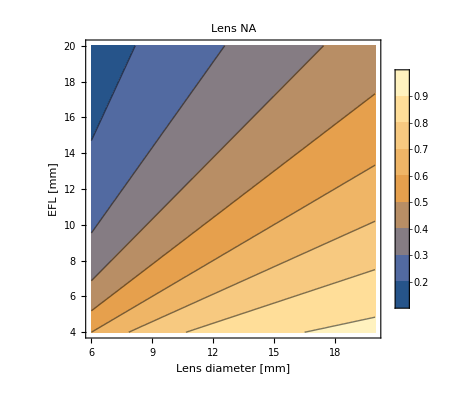

```mathematica
ContourPlot[NA[d,efl],{d,6,20},{efl,4,20},PlotLegends->Automatic, FrameLabel->{"Lens diameter [mm]","EFL [mm]"},PlotLabel-> "Lens NA"]
```

```mathematica
Plot[Evaluate[Table[NA[d,f],{f,{3,4,5}}]],{d,3,10},PlotLegends->Automatic,Frame->True,Axes->False,FrameLabel->{"Collection lens diameter [mm]","NA"},LabelStyle->Directive[Black, Medium]]
```

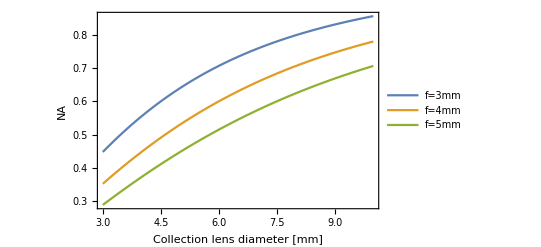

collection as a fraction of the solid angle:

```mathematica
SolidAngle[ϕmax_,θmax_]:= Integrate[Sin[θ],{θ,0,θmax},{ϕ,0,ϕmax}];
```

```mathematica
SolidAngle[2π,π]/(4π)
```

1

```mathematica
θmax=2 ArcTan[d/(2f)]/.{d-> 12,f-> 8}//N;
SolidAngle[θmax,θmax]/(4π)
```

0.0737398

```mathematica
Plot[Evaluate[Table[SolidAngle[ 2ArcTan[d/(2f)],2 ArcTan[d/(2f)]]/(4π),{f,{3,4,5}}]],{d,3,10},PlotLegends->Automatic,Frame->True,Axes->False,FrameLabel->{"Collection lens diameter [mm]","Fractional solid angle"},LabelStyle->Directive[Black, Medium]]
```

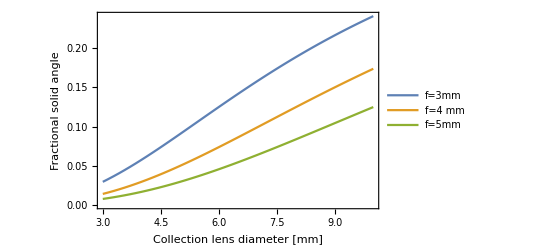

```mathematica
SolidAngle[ 2ArcTan[d/(2f)],2 ArcTan[d/(2f)]]/(4π)/.{d-> 6,f-> 3.3}
```

0.106269

```mathematica
(5*0.0025)/(8*^-4)π
```

49.0874